```mathematica
ClearAll["Global`*"]
```

```mathematica
c1=.05;
c2=.05;
L=.75;
cw=1.;(*0.5以上かな*)
w=2.*π*cw;
k=2.5*π;
```

### Lighthillの式，パラメタの設定

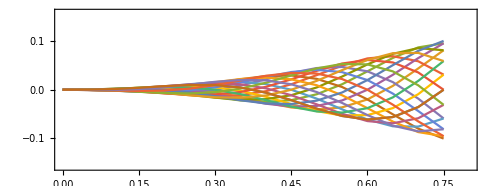

```mathematica
(*Lighthillの式y*)
y[x_,t_,{L_,w_,k_,c1_,c2_}]:=(c1*x/L+c2*(x/L)^2)*Sin[k*(x/L)+w*t]

(*Lighthillの式のパラメタ*)
Module[{},
t=1;
(*プロットしてチェック*)
ListPlot[Table[Table[{x,y[x,t,{L,w,k,c1,c2}]},{x,0,L,.05}],{t,0,2,.1}],
Joined->True,
PlotRange->{{0.,0.8},{-0.16,0.16}},
AspectRatio->(0.3/0.8),
Frame->True]
]
```

### ロボットの形状は各モーターの角度で決まる．その定式化．

```mathematica
(*関節の数，モーターの数n*)
X[0][r_]={0,0};(*左端の関節の座標*)
n=7;
Do[Q[i][r_]={r*Cos[q[i]],r*Sin[q[i]]},{i,0,n,1}]
Do[X[i+1][r_]=X[i][r]+Q[i][r],{i,0,n,1}]
Table[X[i][r],{i,1,n,1}]//MatrixForm
```

(r Cos[q[0]] | r Sin[q[0]]
r Cos[q[0]]+r Cos[q[1]] | r Sin[q[0]]+r Sin[q[1]]
r Cos[q[0]]+r Cos[q[1]]+r Cos[q[2]] | r Sin[q[0]]+r Sin[q[1]]+r Sin[q[2]]
r Cos[q[0]]+r Cos[q[1]]+r Cos[q[2]]+r Cos[q[3]] | r Sin[q[0]]+r Sin[q[1]]+r Sin[q[2]]+r Sin[q[3]]
r Cos[q[0]]+r Cos[q[1]]+r Cos[q[2]]+r Cos[q[3]]+r Cos[q[4]] | r Sin[q[0]]+r Sin[q[1]]+r Sin[q[2]]+r Sin[q[3]]+r Sin[q[4]]
r Cos[q[0]]+r Cos[q[1]]+r Cos[q[2]]+r Cos[q[3]]+r Cos[q[4]]+r Cos[q[5]] | r Sin[q[0]]+r Sin[q[1]]+r Sin[q[2]]+r Sin[q[3]]+r Sin[q[4]]+r Sin[q[5]]
r Cos[q[0]]+r Cos[q[1]]+r Cos[q[2]]+r Cos[q[3]]+r Cos[q[4]]+r Cos[q[5]]+r Cos[q[6]] | r Sin[q[0]]+r Sin[q[1]]+r Sin[q[2]]+r Sin[q[3]]+r Sin[q[4]]+r Sin[q[5]]+r Sin[q[6]])

### ニュートン法を用いた角度の計算 （まずは，最小にしたい関数とヤコビ行列の計算）

```mathematica
Clear[t];
(*inits=Table[RandomReal[{-0.01,0.01}],{i,1,n,1}];(*ニュートン法用の初期値*)*)
(*この関数f[t]を最小とする関節角度は，ロボットはLighthillの曲線の上に乗る*)
f[t_,r_,{L_,w_,k_,c1_,c2_}]=(Table[(#2-y[#1,t,{L,w,k,c1,c2}])^2&@@X[i][r],{i,1,n,1}]);
(*f[t]の微分(ヤコビ行列)*)
DfDq[t_,r_,{L_,w_,k_,c1_,c2_}]=Transpose[Table[D[f[t,r,{L,w,k,c1,c2}],q[i]],{i,0,n-1,1}]];

getSolution[t_,r_,{L_,w_,k_,c1_,c2_},init_]:=Module[{sol,tmp,dq},
(*sol=Table[0,n];*)
sol=init;
Do[
Do[If[Abs[sol[[i+1]]]>80,sol[[i+1]]=0],{i,0,n-1,1}];
tmp=Table[q[i]->sol[[i+1]],{i,0,n-1,1}];
dq=-Dot[Inverse[DfDq[t,r,{L,w,k,c1,c2}]/.tmp],f[t,r,{L,w,k,c1,c2}]/.tmp];
Do[If[Abs[sol[[i+1]]+dq[[i+1]]]<80,sol[[i+1]]+=dq[[i+1]],sol[[i+1]]=0],{i,0,n-1,1}];
If[Norm[dq]<10^-3,Break[]];
,{i,1,10,1}];
(*inits=sol;*)
Return[sol];
]
```

### ライトヒルの式に従う関節角度の時間変化

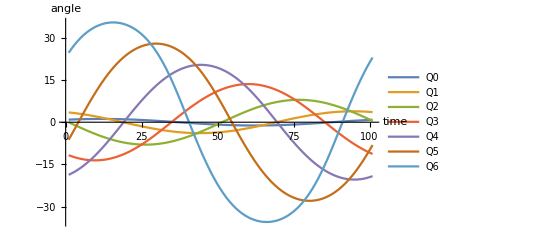

データ総数：101

/Users/tomoaki/Dropbox/markdown/mathematica/魚/each_timeVSangle_c1_0.001_c2_0.1_w1.4.json

```mathematica
(*Lighthillの式のパラメタ*)
(*********************************************************)
n=7;(*モータの数*)
r=L/n;(*各関節の長さ*)
totaldata=100;(*何点計算するか*)
(*********************************************************)
T=1/(w/(2*π));
ans=Table[{t,getSolution[t,r,{L,w,k,c1,c2},Table[RandomReal[{-.1,.1}],n]]},{t,Subdivide[0,N[T-T/totaldata],totaldata]}];
ListPlot[Transpose@Table[ans[[i]][[2]]/Pi*180,{i,1,Length[ans],1}],
Joined->True,
AxesLabel->{"time","angle"},
PlotLegends->{Q0,Q1,Q2,Q3,Q4,Q5,Q6}]
Print["データ総数：",Length[ans]]
(*ListLinePlot[Table[Abs[Fourier[tab[[i]]]],{i,1,n,1}]]*)
(*関節角度の変化を１周期分出力．これをpythonで読み込む*)
Export[FileNameJoin[{NotebookDirectory[],
"each_timeVSangle_c1_"<>ToString[c1]<>"_c2_"<>ToString[c2]<>"_w"<>ToString[cw]<>".json"}],
{"timeVSangle"->ans,
"params"->{"r"->N@r,"L"->N@L,"w"->N@w,"k"->N@k,"c1"->N@c1,"c2"->N@c2}}]
```

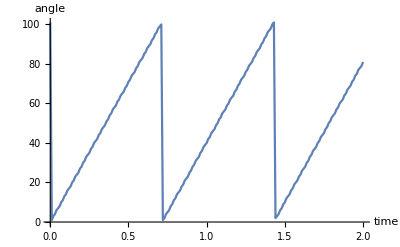

```mathematica
(*時間をデータ番号に変換*)
tToi[tIN_,totaldata_]:=Module[{t,l,s,i},
t=tIN-T*Floor[tIN/T];
i=Round[totaldata*t/T];
If[i==0,i=totaldata];
Return[i]
]
ListPlot[Table[{t,tToi[t,Length[ans]]},{t,0,2,.01}],
Joined->True,
AxesLabel->{"time","angle"}]
```

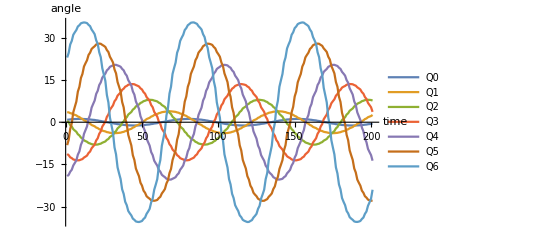

```mathematica
(*時間をデータ番号に変換し，結果を参照する．周期的*)
precalculated[tIN_]:=Module[{t,l,s,i},
i=tToi[tIN,Length[ans]];
Return[ans[[i]][[2]]];
]
ListPlot[Transpose@Table[precalculated[t]/Pi*180,{t,0,2,.01}],
Joined->True,
AxesLabel->{"time","angle"},
PlotLegends->{Q0,Q1,Q2,Q3,Q4,Q5,Q6}]
```

### 時間変化させ，角度を計算し，Lighthillの式と重ねて表示し，確認

```mathematica
If[True(*ここをTrueにしたら動的プロットを表示する*),
s=Table[0,n];
m=Manipulate[
(*Lighthillの式のパラメタ*)
n=7;
r=L/n;(*各関節の長さ*)
s=getSolution[t,r,{L,w,k,c1,c2},Table[0,n]];
replace=Table[q[i]->s[[i+1]],{i,0,n-1,1}];
Table[X[i][r],{i,1,n,1}]/.replace;
(*図１*)
fig1=ListPlot[Table[X[i][r],{i,0,n-1,1}]/.replace,
PlotLegends->{"ロボットの節，モーター"}];
(*図２*)
fig2=ListPlot[Table[X[i][r],{i,0,n,1}]/.replace,Joined->True,PlotStyle->Directive[Blue],PlotLegends->{"ロボット"}];
(*図３*)
fig3=ListPlot[Table[{x,y[x,t,{L,w,k,c1,c2}]},{x,0,L,.01}],Joined->True,PlotStyle->Directive[Red,Dotted],PlotLegends->{"ライトヒルの関数"}];
(*モーターの番号*)
label=ListPlot[(Table[X[i][r],{i,0,n-1,1}]/.replace)->Table[ToString[i],{i,0,n-1,1}]];

(*図を重ねて表示*)
Row[
{StringForm["θ=``",(s/Pi*180)//MatrixForm],
Show[{fig1,fig2,fig3,label},
PlotRange->{{0,1},{-.5,.5}},
Frame->True,
FrameLabel->{"x/L","y"},
GridLines->Automatic,
FrameStyle->Black,
ImageSize->400]}
],
{t,0,5,.1}]
]
```